```mathematica
subG = {gL-> s2W - 1/2,gR-> s2W};
subS2W={s2W-> 0.2324, ds2W-> 0.0083};
```

```mathematica
g1=gL^2;
g2=gR^2;
g3=(gL+1)^2;

(*Processes:A_i values for different scattering processes*)
Aνμ={1,(1-y)^2,0}; (*νμ e->νμ e*)
Aν̄μ={(1-y)^2,1,0}; (*ν̄μ e->ν̄μ e*)
Aνe={0,(1-y)^2,1}; (*νe e->νe e*)
Aν̄e={0,1,(1-y)^2}; (*ν̄e e->ν̄e e*)

(*Differential Cross-Section Function*)
σ[A_]:=(2 GF^2 Me Enu/π) (A[[1]] g1+A[[2]] g2+A[[3]] g3);
σtot[A_]:=Integrate[σ[A],{y,0,1}];
(*Calculate Differential Cross-Sections for each process*)
σνμ=σ[Aνμ];
σν̄μ=σ[Aν̄μ];
σνe=σ[Aνe];
σν̄e=σ[Aν̄e];

σtotνμ=σtot[Aνμ];
σtotν̄μ=σtot[Aν̄μ];
σtotνe=σtot[Aνe];
σtotν̄e=σtot[Aν̄e];
```

```mathematica
σμplus = σν̄μ + σνe//Simplify;
σμminus = σνμ + σν̄e//Simplify;
σtotμplus = σtotν̄μ + σtotνe//Simplify;
σtotμminus = σtotνμ + σtotν̄e//Simplify;
```

```mathematica
Rdiff=(σμplus - σμminus)/(σtotμplus + σtotμminus)/.subG//FullSimplify

Rtot=(σtotμplus - σtotμminus)/(σtotμplus + σtotμminus)/.subG//FullSimplify
```

-(3 s2W (-2+y) y)/(1+8 s2W^2)

(2 s2W)/(1+8 s2W^2)

```mathematica
Integrate[Rdiff,{y,0,1}]
```

(2 s2W)/(1+8 s2W^2)

```mathematica
dRtot=D[Rtot,{s2W}]*ds2W;
dRtot/Rtot/.subS2W
dRdiff=D[Rdiff,{s2W}]*ds2W
```

0.0141633

ds2W ((48 s2W^2 (-2+y) y)/((1+8 s2W^2)^2)-(3 (-2+y) y)/(1+8 s2W^2))

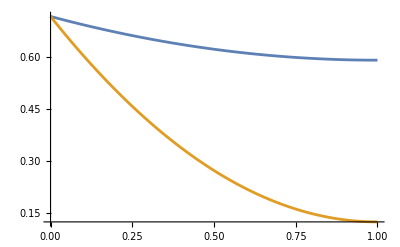

```mathematica
(*Plot[{Rdiff/.subS2W,dRdiff/.subS2W,σμplus/((2 GF^2 Me Enu)/π)},{y,0,1}]//Simplify*)
Plot[{σμplus/((2 GF^2 Me Enu)/π)/.subG/.subS2W,σμminus/((2 GF^2 Me Enu)/π)/.subG/.subS2W},{y,0,1}]//Simplify
```

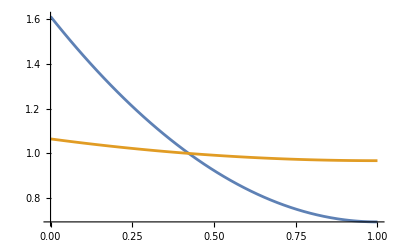

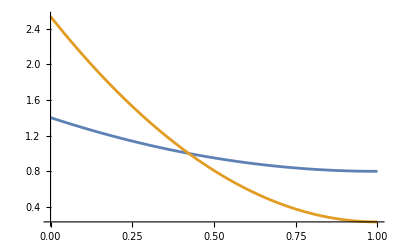

```mathematica
Plot[{(σν̄μ)/(σtotν̄μ)/.subG/.subS2W,σνe/σtotνe/.subG/.subS2W},{y,0,1}]//Simplify
Plot[{σνμ/σtotνμ/.subG/.subS2W,(σν̄e)/(σtotν̄e)/.subG/.subS2W},{y,0,1}]//Simplify
```

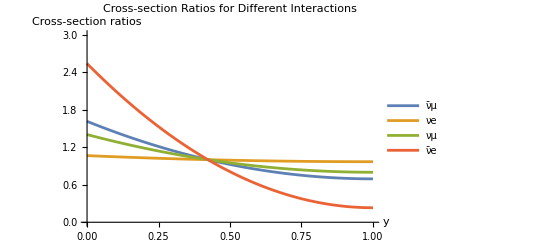

```mathematica
(*First Plot with Legends and Labels*)Plot[{σν̄μ/σtotν̄μ/. subG/. subS2W,σνe/σtotνe/. subG/. subS2W,σνμ/σtotνμ/. subG/. subS2W,σν̄e/σtotν̄e/. subG/. subS2W},{y,0,1},PlotLegends->{"ν̄μ","νe","νμ","ν̄e"},AxesLabel->{"y","Cross-section ratios"},PlotLabel->"Cross-section Ratios for Different Interactions",LabelStyle->Directive[Bold],PlotRange->{{0,1},{0,3}}]//Simplify
```

```mathematica
σμplus/((2 GF^2 Me Enu)/π)
```

1+2 gL+gL^2 (2-2 y+y^2)+gR^2 (2-2 y+y^2)

```mathematica
(σμplus - σμminus)/((2 GF^2 Me Enu)/π)/.y-> Ee/Enu/.subG//FullSimplify
(σμplus - σμminus)/(σμplus + σμminus)/.y-> 1 -(ET2/(2 Me))/.subG//FullSimplify
y(-2+y)/.y-> 1 -(ET2/(2 Me))/.subG//FullSimplify
```

-(2 Ee (Ee-2 Enu) s2W)/Enu^2

-(4 (ET2^2-4 Me^2) s2W)/((ET2^2+4 Me^2) (1+8 s2W^2))

-1+ET2^2/(4 Me^2)

```mathematica
Rdiff/.subS2W/.y-> 1
```

0.486845